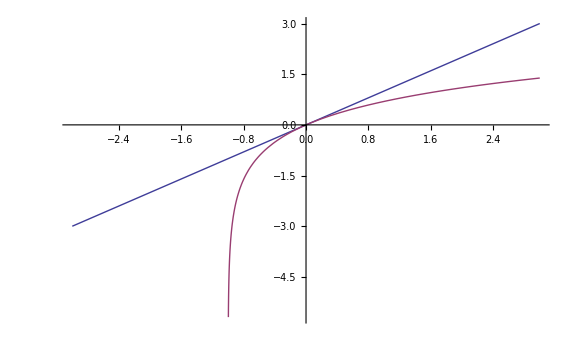

```mathematica
Plot[{x,Log[1+x]},{x,-3,3}]
```

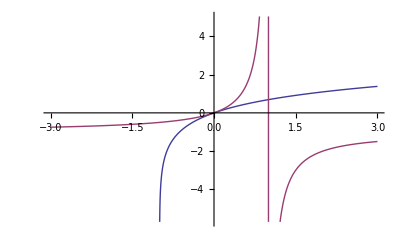

```mathematica
Plot[{Log[1+x],x/(1-x)},{x,-3,3}]
```

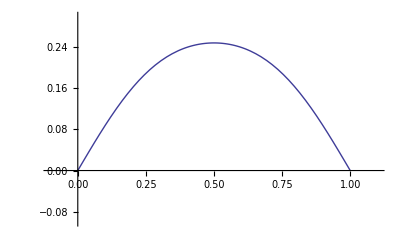

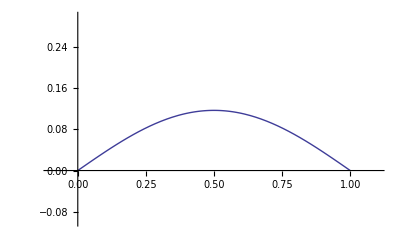

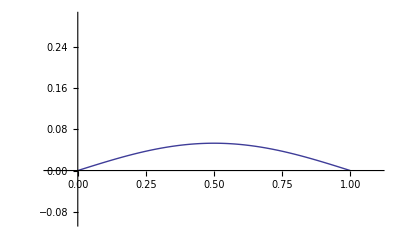

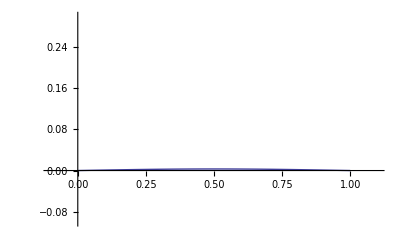

```mathematica
u0[x_]:=x(1-x);
u[N_,x_,t_,l_,k_]:=Sum[(2/l)Integrate[u0[y]Sin[(n Pi y )/l],{y,0,l}]Exp[-((k n Pi)/l)^2 t]Sin[n Pi x/l ],{n,1,N}];
graphu[N_,t_,l_,k_]:= Plot[Evaluate[u[N,x,t,l,k]],{x,0,l},PlotRange->{{-.1,1.1},{-.1,.3}}];
graphu[3,0,1.0,.2]
graphu[3,2,1.0,.2]
graphu[3,4,1.0,.2]
graphu[15,5,1.0,.3]
```

```mathematica
anim[N_,l_,k_,tmax_]:=Animate[graphu[N,t,l,k],{t,0,tmax},AnimationRunning->False];
anim[10,1,.2,10]
```

```mathematica
Integrate[Cos[6Pi t /3] Cos[6Pi t /3],{t,-3,3}]
```

3